```mathematica
(* 4: rhoin, iein, Byin=By, Bxin=0, vxin=vx, vyin=0 *)
```

```mathematica
(* 2: rhoc, iec, Bxc=Byc=0, vxc=vyc=0 *)
```

```mathematica
(* 4: rhoout, ieout, Bxout=Bx, Byout=0, vyout=vy, vxout=0 *)

(* 1 : d *)
```

```mathematica
(* 11 total variables *)
(* 3: rhoin, iein, Byin considered knowns *)
(* 8 unkonwns: d,vx,rhoc,iec,rhout,ieout,Bx,vy *)
(* So we need 8 equations *)
```

```mathematica
(* Aux variables: Ez, Jz, np *)
```

```mathematica
(* UpperRight x-y quad: sign[By]=sign[Bx] and sign[vx]=-sign[vy] *)
(* UpperLeft x-y quad: sign[By]=-sign[Bx] and sign[vx]=sign[vy] *)
(* LowerRight x-y quad: sign[By]=-sign[Bx] and sign[vx]=sign[vy] *)
(* LowerLeft x-y quad: sign[By]=sign[Bx] and sign[vx]=-sign[vy] *)
```

```mathematica
(* correct even in relativistic steady case *)
auxvars={etap->eta*4*Pi/c^2,Ez->etap*Jz,Jz->(c/(4*Pi))*(Bx/L-By/d)}
(* L>>d *)
(*auxvars={etap->eta*4*Pi/c^2,Ez->etap*Jz,Jz->(c/(4*Pi))*(-By/d)}*)
```

{etap→(4 eta π)/c^2,Ez→etap Jz,Jz→(c (-By/d+Bx/L))/(4 π)}

```mathematica
(* E_z dissipation at center *)
(* ideal MHD outside each face *)
(* E_z constant *)
```

```mathematica
(* correct even in relativistic case *)
```

```mathematica
(*myfun[x_]:=Abs[x]*)
myfun[x_]:=x
```

```mathematica
eq1=(myfun[-Ez-vx*By/c])//.auxvars
eq2=(myfun[-Ez+vy*Bx/c])//.auxvars
```

(By eta)/(c d)-(By vx)/c

(By eta)/(c d)+(Bx vy)/c

```mathematica
(* x-momentum flux dissipates completely, then y-momentum is created *)
(* C=(rho + u + p + bsq)v^i v^j + (bsq/2+pg)\delta^i_j - b^i b_j *)
(* along x-direction:  *)
(* C=(rho + u + p + bsq)v^x v^x + bsq/2+p - b^x b_x *)
(* no stress *)
(* C=(rho + u + p + bsq)vx^2 + bsq/2+p *)
(* from in to c *)
pin=(gam-1)*iein
pc=(gam-1)*iec
pout=(gam-1)*ieout
gamx=1/Sqrt[1-(vx/c)^2];gamxgamxm1=gamx*(gamx-1);
gamx=1;gamxgamxm1=vx^2/2;
ux=vx*gamx
gamy=1/Sqrt[1-(vy/c)^2];gamygamym1=gamy*(gamy-1);
gamy=1;gamygamym1=vy^2/2
uy=vy*gamy
(* b^i = (B^i + b^t u^i)/u^t = B^i/u^t + b^t v^i = B^i/u^t + B^j u^t v^j v^i ;  b^t = B^i u_i = B^i u^t v^i *)
(*btin=0 (* since perp *)*)
(*btout=0 (* since perp *)*)
by=By/gamx
bx=Bx/gamy
bsqin=by^2
bsqout=bx^2
(*eq3=(By^2/(8*Pi)+pin)==pc*)
(* -bx*bx/(4*Pi) *)
eq3=myfun[(rhoin+(iein+pin+bsqin/(4*Pi))/c^2)*ux^2+(bsqin/(8*Pi)+pin)-pc]
(*eq3=(By^2/2+0)==pc*)
(* from in to out *)
(* bsqin/2 + pin = (rhoout + uout + pout + bsqout)vx^2 + bsqout/2+pout *)
(* By^2/2 + (gam-1)*iein == (rhoout + gam*ieout + 0)vy^2 + 0 + (gam-1)ieout *)
(*eq4=pc *dz*L*d== ((rhoout + gam*ieout)*vy^2 +pout)*dz*d*)
(* non-rel *)
(*eq4=pc== ((rhoout)*vy^2 +pout)*)
(* -bx*bx/(4*Pi) *)
eq4=myfun[-pc+ (rhoout + (ieout+pout+bsqout/(4*Pi))/c^2)*uy^2 +(bsqout/(8*Pi)+pout)]
```

(-1+gam) iein

(-1+gam) iec

(-1+gam) ieout

vx

vy^2/2

vy

By

Bx

By^2

Bx^2

-(-1+gam) iec+(-1+gam) iein+By^2/(8 π)+((iein+(-1+gam) iein+By^2/(4 π))/c^2+rhoin) vx^2

-(-1+gam) iec+(-1+gam) ieout+Bx^2/(8 π)+((ieout+(-1+gam) ieout+Bx^2/(4 π))/c^2+rhoout) vy^2

```mathematica
(* rest mass conservation: applies to UpperRight quad *)
eq5=myfun[rhoin*c*(-ux)*L*dz-rhoout*c*uy*d*dz]
```

-c dz L rhoin vx-c d dz rhoout vy

```mathematica
(* assumption by Dmitri *)
(* Dmitri version *)
eq6=myfun[rhoc-rhoout]
(* jon version *)
(*uth=Sqrt[2*iec/rhoc]
eq6=myfun[uth*rhoc-vy*rhoout]*)
(* jon test *)
(*eq6=rhoc==(1/2)*rhoout*)
```

rhoc-rhoout

```mathematica
(* energy conservation *)
(* -rho u_t + (rho+u+p+bsq)u^i u_t - b^i b_t *)
(* (1/2*rho*v^2 + u+p+bsq)*v^i - b^i b_t *)
(* assume no stress , and no incoming inertia not dominating *)
```

```mathematica
(* 0\sim (1/2)*rhoin*vx^2 *)
```

```mathematica
(*eq7=( (1/2)*rhoin*vx^2+iein + pin+By^2/(4*Pi))*vx  * L * dz== ( (1/2)*rhoout*vy^2+ieout+pout+Bx^2/(4*Pi))*vy * d * dz *)
(*eq7=( By^2)*vx  * L * dz== ( (1/2)*rhoout*vy^2+pout)*vy * d * dz*)
(* Applies to UpperRight quad *)
eq7=myfun[(( rhoin*gamxgamxm1*c^2+iein +pin+bsqin/(4*Pi))*(-ux)*gamx  * L * dz)-(( rhoout*gamygamym1+ieout+pout+bsqout/(4*Pi))*uy*gamy* d * dz)]
```

-dz L vx (iein+(-1+gam) iein+By^2/(4 π)+1/2 c^2 rhoin vx^2)-d dz vy (ieout+(-1+gam) ieout+Bx^2/(4 π)+(rhoout vy^2)/2)

```mathematica
(* Dmitri assumption *)
(* -- below equivalent to pin=pout *)
(*eq8=pc-pout==pin+bsqin/(8*Pi)*)
(* other choices *)
(*eq8=pc-pout==0 -- not allowed?*)
(*eq8=pout==pc/4.7*)
(* Dmitri assumption *)
eq8=myfun[(pc-pout)-(bsqin/(8*Pi))]
```

(-1+gam) iec-(-1+gam) ieout-By^2/(8 π)

```mathematica
(* Setup inflow conditions *)
consts={By->1,c->10^5,L->1,eta->10^(-5),rhoin->1000,iein->0,gam->5/3,dz->1}
```

{By→1,c→100000,L→1,eta→1/100000,rhoin→1000,iein→0,gam→5/3,dz→1}

```mathematica
(* Check if setup magnetically-dominated *)
(By^2/(8*Pi)-(pin))//.consts
(* Original SP solution: Used as initial guess, since otherwise can miss finding solution for some inflow values for no good reason *)
(* original SP delta: delta = (eta L/va)^(1/2) *)
vaold=c*By/Sqrt[1*4*Pi*(rhoin*c^2+iein+pin+By^2/(4*Pi))]//.consts
olddelta=Sqrt[eta*L/vaold]//.consts
S=L*vaold/eta//.consts
(* UpperRight quad *)
vxold=-(vaold*S^(-1/2))
rhoold=rhoin//.consts
ieold=iein//.consts
(* UpperRight quad *)
Bxold=-By*vxold/vaold//.consts (* guess on Ez=constant *)
olddelta=1.0*Sqrt[eta*L/vaold]//.consts
vextreme=1-10^(-5)
```

1/(8 π)

50000/(√((10000000000000+1/(4 π)) π))

((10000000000000+1/(4 π)) π)^(1/4)/(50000 √2)

5000000000/(√((10000000000000+1/(4 π)) π))

-1/(√2 ((10000000000000+1/(4 π)) π)^(1/4))

1000

0

((10000000000000+1/(4 π)) π)^(1/4)/(50000 √2)

0.0334813

99999/100000

```mathematica
eqns={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
(*myeqns=FullSimplify[eqns,{d>0,vx<0,rhoc>0,iec>0,rhoout>0,ieout>0,Bx>0,vy>0}];*)
myeqns=eqns;
eqns0={eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,eq8==0};
(*myeqns0=FullSimplify[eqns0,{d>0,vx<0,rhoc>0,iec>0,rhoout>0,ieout>0,Bx>0,vy>0}];*)
myeqns0=eqns0;
nummyeqns0=myeqns0//.consts;
```

```mathematica
(* NSolve didn't work even for simple SP case *)
(*fsols=NSolve[nummyeqns0,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]*)
```

```mathematica
(*(* can find solution, but can be too complicated looking *)
fsols=Solve[eqns0,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]*)
```

```mathematica
(* Break[]; *)
```

```mathematica
fsols=NSolve[nummyeqns0,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}];
Dimensions[fsols]
For[i=1,i≤Dimensions[fsols][[1]],i++,
whichi=i;
If[Re[fsols[[i,1,2]]]>0&&Re[fsols[[i,1,2]]]<(L//.consts)&&Abs[Im[fsols[[i,1,2]]]]<10^(-13)*Abs[Re[fsols[[i,1,2]]]],mysol=fsols[[i]];];
Print[Im[fsols[[i,1,2]]]];
Print[Re[fsols[[i,1,2]]]];
Print[i];
];
mysol
Print["Picked i="];
whichi
errorvec=myeqns//.consts//.mysol;
Print["Error="];
error=errorvec.errorvec
```

{12,8}

0

-18.7921

1

-15.9754

-8.89606

2

15.9754

-8.89606

3

15.9754

8.89606

4

-15.9754

8.89606

5

0

18.7921

6

0

-0.631077

7

-0.546529

-0.315528

8

0.546529

-0.315528

9

0.546529

0.315528

10

-0.546529

0.315528

11

0

0.631077

12

{d→0.631077,vx→0.0000158459,rhoc→0.0158457,iec→0.0596835,rhoout→0.0158457,ieout→3.7664×10^-7,Bx→9.99984×10^-6,vy→-1.58462}

Picked i=

12

Error=

5.16988×10^-26

```mathematica
(*(* only finds 1 root and only if numerical otherwise from variables *)FindInstance[nummyeqns0 ,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy},Reals]*)
```

```mathematica
(* Form initial guess from NSolve since otherwise has problems *)
myvars={{d,dvar},{vx,vxvar},{rhoc,rhocvar},{iec,iecvar},{rhoout,rhooutvar},{ieout,ieoutvar},{Bx,Bxvar},{vy,vyvar}}//.{dvar->mysol[[1,2]],vxvar->mysol[[2,2]],rhocvar->mysol[[3,2]],iecvar->mysol[[4,2]],rhooutvar->mysol[[5,2]],ieoutvar->mysol[[6,2]],Bxvar->mysol[[7,2]],vyvar->mysol[[8,2]]}
```

{{d,0.631077},{vx,0.0000158459},{rhoc,0.0158457},{iec,0.0596835},{rhoout,0.0158457},{ieout,3.7664×10^-7},{Bx,9.99984×10^-6},{vy,-1.58462}}

```mathematica
fsols=FindRoot[nummyeqns0,myvars,WorkingPrecision->20,MaxIterations->1000]
(*fsols=FindRoot[nummyeqns0,{{d,olddelta},{vx,vxold},{rhoc,rhoold},{iec,ieold},{rhoout,rhoold},{ieout,ieold},{Bx,Bxold},{vy,vaold}},WorkingPrecision->20,MaxIterations->1000]*)
(* MaxIterations->10000,WorkingPrecision->50] *)
result=myeqns//.consts//.fsols
error=Sqrt[result.result]
```

{d→0.63107686168040522311,vx→0.000015845930356838651866,rhoc→0.01584567817499671004,iec→0.059683480299724063142,rhoout→0.01584567817499671004,ieout→3.7664026331067400595×10^-7,Bx→9.9998408538746150153×10^-6,vy→-1.5846182542694033778}

{-1.3×10^-27,-7.49×10^-27,-1.04×10^-18,5.16×10^-18,4.×10^-15,0.,-7.5×10^-19,1.04×10^-18}

4.×10^-15

```mathematica
(* DampingFactor->1000,MaxIterations->1000, *)
```

```mathematica
{res,{evx}}=Reap[FindRoot[nummyeqns0,{{d,olddelta},{vx,vxold},{rhoc,rhoold},{iec,ieold},{rhoout,rhoold},{ieout,ieold},{Bx,Bxold},{vy,vaold}},WorkingPrecision->20,MaxIterations->10000,DampingFactor->0.1,EvaluationMonitor:>Sow[{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]]];
(*Clear[res,evx]
{res,{evx}}=Reap[FindRoot[nummyeqns0,{{d,0.0001,0.1},{vx,-.99,-.0001},{rhoc,.01,200},{iec,0.001,100},{rhoout,0.01,200},{ieout,0.00001,100},{Bx,0.0001,0.3},{vy,0.01,0.999}},MaxIterations->1000,WorkingPrecision->20,Method->"Secant",EvaluationMonitor:>Sow[{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]]];*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

```mathematica
res
result=myeqns//.consts//.res
error=Sqrt[result.result]
```

{d→0.0294022,vx→-0.0000931484,rhoc→0.447014,iec→0.0640604,rhoout→0.447014,ieout→0.00998248,Bx→0.00275499,vy→0.272445}

{0.00349398,0.00415141,0.00374846,0.00112274,-0.00362843,0.,-0.000293048,-0.00373678}

0.00848343

```mathematica
evx[[1]]
evx[[2]]
evx[[3]]
evx[[97]]
evx[[100]]
```

{0.19265455739176799367,-0.0051906376549736858808,1.,0.01,1.,0.01,0.019265455739176799367,0.26942719265230724909}

{-0.16094828404258520741,0.013700161652544437683,-0.12017588136346979291,0.19732334663528923353,-0.12017588136346979291,0.0098166939065731022322,-0.046669378075924685088,0.21097219683153184414}

{0.053033097865209252582,0.0022684680474578710631,0.5576941891982705566,0.083965353203967841765,0.5576941891982705566,0.00992762087487601069,-0.0067691702654184109868,0.24634600982015300203}

{-0.030760411298319815519,0.0036567730367786103713,0.85266147665365022725,0.070290897102806686603,0.85266147665365022725,0.0099975835201630807315,-0.016168124972829681036,0.20105318323966318956}

{0.69757211935475867628,-0.073333827038405417396,16.528167641777097646,0.069398504007472155286,16.528167641777097646,0.0090716169420335443513,0.22696129586323028155,-1.5373486762560522688}

```mathematica
(* CHECK CONVERGENCE *)
```

{135,8}

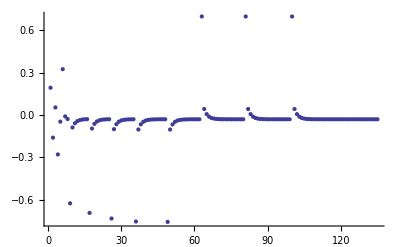

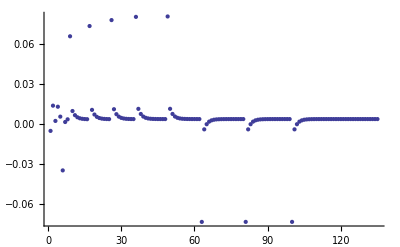

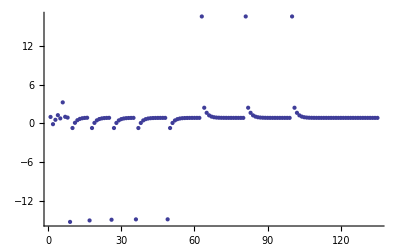

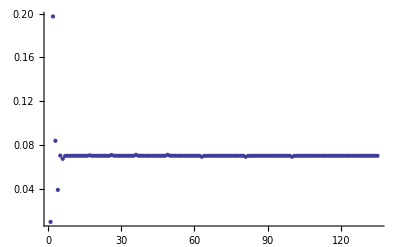

-Graphics-

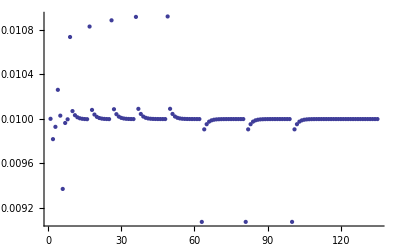

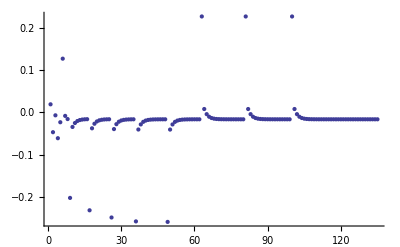

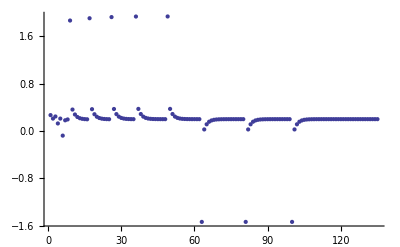

```mathematica
dim=Dimensions[evx]
which=1;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=2;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=3;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=4;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=5;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=6;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=7;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=8;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
```

```mathematica
(* http://www.scipy.org/ *)
```

```mathematica
(*fsols=FindRoot[eqns,{{d,0.0001,1},{vx,-.999,0},{rhoc,.01,100},{iec,0.001,100},{rhoout,0.01,100},{ieout,0.01,100},{Bx,0.01,100},{vy,0,0.999}},MaxIterations->10000,DampingFactor->1.5,WorkingPrecision->20,Method->"Secant"]*)
```

```mathematica
(*fsols=FindRoot[eqns,{{d,0.001*olddelta,1},{vx,-vextreme,vextreme},{rhoc,.1*rhoold,10*rhoold},{iec,0.1*ieold,10*ieold},{rhoout,0.1*rhoold,10*rhoold},{ieout,0.1*ieold,10*ieold},{Bx,0.01*Bxold,10*Bxold},{vy,-vextreme,vextreme}},MaxIterations->10000,DampingFactor->1.5,WorkingPrecision->20,Method->"Brent"]*)
```

```mathematica
vaold2=c*By/Sqrt[1.0*4*Pi*rhoout*c^2]//.consts//.fsols
olddelta=Sqrt[eta*L/vaold2]//.consts//.fsols
olddelta=1.0*Sqrt[eta*L/vaold]//.consts//.fsols
```

0.117926

0.0291202

0.039864

```mathematica
gamx//.consts//.fsols
gamy//.consts//.fsols
(rhoc/rhoin)//.consts//.fsols
(rhoout/rhoc)//.consts//.fsols
```

1.00004

1.00933

5.54579

1.

```mathematica
(* Check that numerical satisfies original equations *)
result=eqns//.consts//.fsols
```

{0.202754,0.195468,-0.00359482,-0.003376,0.0156682,0.,0.000179738,1.44814×10^-6}

```mathematica
(* DONE! *)
```

```mathematica
(* DONE! with numerical result *)
```

```mathematica
(* ANALYTICAL: try to get analytic solution: Works only if remove extra non-Dmitri terms *)
```

```mathematica
eqns={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
sols=Solve[eqns,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}];
eqnsother={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8}//.{iein->0};
solsother=Solve[eqnsother,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}];
```

$Aborted

$Aborted

```mathematica
sols//.consts
solsother//.consts
```

{{rhoc→3.83333,Bx→-0.0103024,iec→0.95,vx→-0.0037208,rhoout→3.83333,ieout→0.2,d→-0.0268759,vy→0.361158},{rhoc→3.83333,Bx→-0.0103024 ⅈ,iec→0.95,vx→0.0037208 ⅈ,rhoout→3.83333,ieout→0.2,d→-0.0268759 ⅈ,vy→-0.361158},{rhoc→3.83333,Bx→0.0103024 ⅈ,iec→0.95,vx→-0.0037208 ⅈ,rhoout→3.83333,ieout→0.2,d→0.0268759 ⅈ,vy→-0.361158},{rhoc→3.83333,Bx→0.0103024,iec→0.95,vx→0.0037208,rhoout→3.83333,ieout→0.2,d→0.0268759,vy→0.361158}}

{{rhoc→5/2,Bx→-0.00747674,iec→3/4,vx→-0.0033437,rhoout→5/2,ieout→0,d→-0.029907,vy→1/(√5)},{rhoc→5/2,Bx→-0.00747674 ⅈ,iec→3/4,vx→0.0033437 ⅈ,rhoout→5/2,ieout→0,d→-0.029907 ⅈ,vy→-1/(√5)},{rhoc→5/2,Bx→0.00747674 ⅈ,iec→3/4,vx→-0.0033437 ⅈ,rhoout→5/2,ieout→0,d→0.029907 ⅈ,vy→-1/(√5)},{rhoc→5/2,Bx→0.00747674,iec→3/4,vx→0.0033437,rhoout→5/2,ieout→0,d→0.029907,vy→1/(√5)}}

```mathematica
(*
eqnsraw={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
array=CoefficientArrays[eqnsraw,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]
mymatrix=Normal[array][[2]]
myb==Normal[array][[1]]
Det[mymatrix]
*)
```

```mathematica
(*
array=CoefficientArrays[eqns,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]
mymatrix=Normal[array][[2]]
myb==Normal[array][[1]]
Det[mymatrix]
*)
```

```mathematica
(*mymatrix.{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}*)
```

```mathematica
(*NSolve[mymatrix.{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}==myb,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]*)
```

```mathematica
(*array=CoefficientArrays[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{vx,rhoc,iec,rhout,ieout,Bx,vy}]
Normal[array]*)
```

```mathematica
(*
eq1=x*1==2
eq2=y*3==5
eqns={eq1,eq2}
array=CoefficientArrays[eqns,{y,x}]
MatrixForm[Normal[array]]
N[Det[Normal[array]]]
*)
```

```mathematica
(*
mymatrix=Normal[array][[2]]
MatrixForm[mymatrix]
Det[mymatrix]
*)
```